```mathematica
f[x_]:=1/2(1+Tanh[10.*x])
```

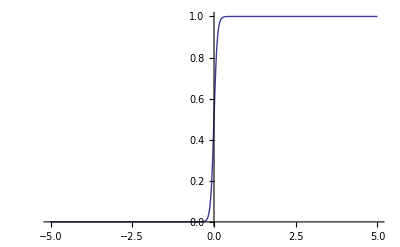

```mathematica
Plot[f[x],{x,-5,5}]
```

```mathematica
x=-5.;While[x<5,Print[x,",",f[x]];x=x+0.1]
```

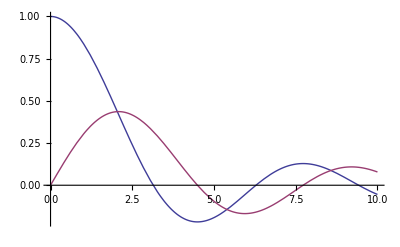

```mathematica
g[x_]:=SphericalBesselJ[0,x]
h[x_]:=SphericalBesselJ[1,x]
Plot[{g[x],h[x]},{x,0,10}]
```

```mathematica
x=0.;While[x<10,Print[x,",",g[x]",",h[x]];x=x+0.1]
```

0.,1. ,0.

0.1,0.998334 ,0.0333

0.2,0.993347 ,0.0664004

0.3,0.985067 ,0.0991029

0.4,0.973546 ,0.131212

0.5,0.958851 ,0.162537

0.6,0.941071 ,0.192892

0.7,0.920311 ,0.222098

0.8,0.896695 ,0.249986

0.9,0.870363 ,0.276393

1.,0.841471 ,0.301169

1.1,0.810189 ,0.324175

1.2,0.776699 ,0.345285

1.3,0.741199 ,0.364384

1.4,0.703893 ,0.381375

1.5,0.664997 ,0.396173

1.6,0.624734 ,0.408708

1.7,0.583332 ,0.418927

1.8,0.541026 ,0.426794

1.9,0.498053 ,0.432285

2.,0.454649 ,0.435398

2.1,0.411052 ,0.436142

2.2,0.367498 ,0.434545

2.3,0.32422 ,0.43065

2.4,0.281443 ,0.424515

2.5,0.239389 ,0.416213

2.6,0.19827 ,0.40583

2.7,0.158289 ,0.393467

2.8,0.119639 ,0.379236

2.9,0.0824998 ,0.363261

3.,0.04704 ,0.345677

3.1,0.0134131 ,0.326628

3.2,-0.0182419 ,0.306267

3.3,-0.0478017 ,0.284751

3.4,-0.0751591 ,0.262247

3.5,-0.100224 ,0.238924

3.6,-0.122922 ,0.214954

3.7,-0.143199 ,0.190514

3.8,-0.161015 ,0.165777

3.9,-0.17635 ,0.140918

4.,-0.189201 ,0.116111

4.1,-0.19958 ,0.091523

4.2,-0.207518 ,0.0673197

4.3,-0.213062 ,0.0436598

4.4,-0.216273 ,0.0206954

4.5,-0.217229 ,-0.00142958

4.6,-0.21602 ,-0.0225798

4.7,-0.21275 ,-0.04263

4.8,-0.207534 ,-0.0614653

4.9,-0.200501 ,-0.0789822

5.,-0.191785 ,-0.0950894

5.1,-0.181532 ,-0.109708

5.2,-0.169895 ,-0.122771

5.3,-0.157032 ,-0.134228

5.4,-0.143105 ,-0.144037

5.5,-0.12828 ,-0.152173

5.6,-0.112726 ,-0.158624

5.7,-0.0966115 ,-0.16339

5.8,-0.0801038 ,-0.166487

5.9,-0.0633689 ,-0.16794

6.,-0.0465692 ,-0.16779

6.1,-0.0298627 ,-0.166087

6.2,-0.0134015 ,-0.162894

6.3,0.00266887 ,-0.158284

6.4,0.0182108 ,-0.15234

6.5,0.0330954 ,-0.145153

6.6,0.0472032 ,-0.136823

6.7,0.0604254 ,-0.127456

6.8,0.0726637 ,-0.117167

6.9,0.0838318 ,-0.106071

7.,0.0938552 ,-0.0942924

7.1,0.102672 ,-0.0819542

7.2,0.110232 ,-0.0691833

7.3,0.116498 ,-0.0561068

7.4,0.121447 ,-0.0428514

7.5,0.125067 ,-0.0295425

7.6,0.127358 ,-0.0163029

7.7,0.128334 ,-0.00325199

7.8,0.128018 ,0.00949525

7.9,0.126448 ,0.0218292

8.,0.12367 ,0.0336462

8.1,0.119739 ,0.0448498

8.2,0.114723 ,0.055351

8.3,0.108695 ,0.0650689

8.4,0.101738 ,0.0739317

8.5,0.0939397 ,0.0818767

8.6,0.085395 ,0.0888506

8.7,0.0762034 ,0.0948103

8.8,0.0664679 ,0.0997228

8.9,0.0562945 ,0.103565

9.,0.0457909 ,0.106325

9.1,0.0350658 ,0.107999

9.2,0.0242272 ,0.108595

9.3,0.0133822 ,0.10813

9.4,0.00263568 ,0.106631

9.5,-0.00791064 ,0.104133

9.6,-0.018159 ,0.10068

9.7,-0.0280166 ,0.0963246

9.8,-0.0373958 ,0.0911256

9.9,-0.0462157 ,0.085149

```mathematica
x={0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0}
y={1.67203,1.79792,2.37791,2.66408,2.11245,2.43969,1.88843,1.59447,1.79634,1.07810,0.21066}
sum=0
x[[2]]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

{1.67203,1.79792,2.37791,2.66408,2.11245,2.43969,1.88843,1.59447,1.79634,1.0781,0.21066}

0

0.1

```mathematica
sumX=Total[x]
sumXX=Total[x^2]
sumXXX=Total[x^3]
sumXXXX=Total[x^4]
sumY=Total[y]
sumXY=Total[x*y]
sumXXY=Total[x^2*y]
```

5.5

3.85

3.025

2.5333

19.6321

8.38663

4.99548

```mathematica
a={{11,5.5,3.85},{5.5,3.85,3.025},{3.85,3.025,2.5333}}
b={19.6321,8.38663,4.99548}
```

{{11,5.5,3.85},{5.5,3.85,3.025},{3.85,3.025,2.5333}}

{19.6321,8.38663,4.99548}

```mathematica
LeastSquares[a,b]
```

{1.65417,3.90257,-5.20204}